# Equivariant Polynomial Tensor Functions

Michael Liu

## Abstract

We present an algorithm to enumerate a vector space basis for the covariant module of harmonic-tensor-valued SO(3)-equivariant polynomial functions on harmonic tensors. Our approach is to compute the isotypic (irreducible) decomposition of the symmetric power of a finite dimensional SO(3)-representation using Schur-Weyl duality and Clebsch-Gordan theory.

We then present closely related algorithms to enumerate 1) a module basis for the covariant module over the invariant ring and 2) an algebra basis for the invariant ring. Our approach is to build generators degree by degree using the previous algorithm and Nakayama’s lemma.

We implement our algorithms in the special case where the polynomial functions take harmonic tensor inputs of order and multiplicity at most 3.

## Problem Statement

Let G:=SO(3), let X be any finite dimensional G-representation, and let Y be any irreducible G-representation. Let (𝒮(X^*)⊗Y)^G be the module of covariants, i.e., the space of equivariant polynomial functions from X to Y (see Lemma A1). Let (𝒮(X^*))^G be the ring of invariants, i.e., the space of invariant polynomial functions from X to ℂ. Our first goal is to enumerate vector space bases for the covariant module and the invariant ring. We introduce the necessary tools in the Preliminaries section below.

## Preliminaries

### Isotypic Decomposition

Our approach is essentially to compute the isotypic (irreducible) decomposition of the graded pieces of the covariant module and the invariant ring. Towards this, the main difficulty is to compute the isotypic decomposition of the symmetric tensor power 𝒮^D(X) of the input space X.

#### Theorem (Isotypic decomposition)

Let Z be any finite dimensional G-representation, let Λ:=ℕ_0 be the set of irrep labels for G, and let H_λ be the G-irrep of dimension 2λ+1. Then

Z≅⊕_λϵΛ H_λ⊗Hom_G(H_λ,Z),

where the action of G on the right-hand-side is only on the H_λ factors.

#### Remark (Isotypic decomposition of the symmetric power 𝒮^D(X))

By the above, the symmetric power 𝒮^D(X) has the isotypic decomposition

𝒮^D(X)≅⊕_(ν∈Λ)H_ν⊗Hom_G(H_ν,𝒮^D(X)).

Our main subroutine is to enumerate a vector space basis for the multiplicity space Hom_G(H_ν,𝒮^D(X)).

### Clebsch-Gordan Theory

To accomplish the above, we rely heavily on the well established Clebsch-Gordan theory for SO(3), which describes how to compute the isotypic decomposition of the tensor product of SO(3) irreps.

#### Definition (Clebsch-Gordan coefficient)

For any λ_1,λ_2,λ_3∈Λ and any m_1,m_2,m_3∈ℤ, we denote by

(λ_1 | λ_2 | λ_3
m_1 | m_2 | m_3)∈ℝ

the corresponding Clebsch-Gordan coefficient, which can be computed using software such as Mathematica’s ClebschGordan function.

#### Definition (Clebsch-Gordan tensor)

For any λ:=(λ_1,…,λ_d),γ:=(γ_1,…,γ_d)∈Λ^d such that λ_1=γ_1, the Clebsch-Gordan tensor is

CG(λ,γ):=∏_(j=1)^(d-1) (γ_j | λ_(j+1) | γ_(j+1)
s_j | m_(j+1) | s_(j+1))∈ℝ^(2 λ_1+1)⊗…⊗ℝ^(2 λ_d+1)⊗ℝ^(2 γ_d+1),

where s_j:=m_1+…+m_j, and the free indices are m_1,…,m_d along with the last index s_d, which is completely determined by the m_j.

#### Lemma (Tensor train factorization of the Clebsch-Gordan tensor)

The Clebsch-Gordan tensor CG(λ,γ) has the tensor train factorization

CG(λ,γ)=∏_(j=1)^(d-1) CG((γ_j,λ_(j+1)),(γ_j,γ_(j+1))),

where the product ∏_(j=1)^(d-1)  denotes tensor contraction. Include an illustration here.

#### Remark

The Clebsch-Gordan tensor CG(λ,γ) can be viewed as an element of H_λ_1⊗…⊗H_λ_d⊗H_γ_d by fixing the angular momentum basis (see Lemma A3) on each irrep H_λ. Since H_λ≅H_λ^*, we can also view CG(λ,γ) as an element of Hom(H_γ_d,H_λ_1⊗…⊗H_λ_d). In fact, all Clebsch-Gordan tensors are G-equivariant, i.e., we have CG(λ,γ)∈Hom_G(H_γ_d,H_λ_1⊗…⊗H_λ_d). Thus, one might expect that the Clebsch-Gordan tensors play a role in the isotypic decomposition of the tensor product of G-irreps. Indeed this is the case, as summarized below.

#### Theorem (Isotypic decomposition of the tensor product of two G-irreps)

Let H_λ_1,H_λ_2 be G-irreps. Then

H_λ_1⊗H_λ_2≅⊕_(γ_2=|λ_1-λ_2|)^(λ_1+λ_2)H_γ_2⊗Hom_G(H_γ_2,H_λ_1⊗H_λ_2).

Moreover, a basis for Hom_G(H_γ_2,H_λ_1⊗H_λ_2) is given by the single Clebsch-Gordan tensor CG(λ,γ), where λ=(λ_1,λ_2) and γ=(λ_1,γ_2).

#### Theorem (Isotypic decomposition of the tensor product of multiple G-irreps)

Let H_λ_1,...,H_λ_d be G-irreps. Then

H_λ_1⊗…⊗H_λ_d≅⊕_(μ=Max[0,2m-s])^s H_μ⊗Hom_G(H_μ,H_λ_1⊗…⊗H_λ_d),

where s:=λ_1+…+λ_d and m:=Max[λ_1,…,λ_d]. Moreover, a basis for Hom_G(H_μ,H_λ_1⊗…⊗H_λ_d) is given by the Clebsch-Gordan tensors CG(λ,γ), where λ=(λ_1,…,λ_d) and γ ranges over all γ∈Λ^d such that CG(λ,γ) is nonzero.

### Symmetrization

Finally, Schur-Weyl duality appears in our proofs, so we need to introduce Young symmetrizers.

#### Definition (Young symmetrizer)

Let π be an integer partition of d, and let T_π be the associated standard Young tableau filled in English-reading order. Define

R_π:={σ∈𝔖^d|σ preserves every row of T_π},
C_π:={σ∈𝔖^d|σ preserves every column of T_π}.

The row, column, and Young symmetrizers are

r_π:=1/(|R_π|)∑_(σ∈R_π) σ,
c_π:=1/(|C_π|)∑_(σ∈C_π) sgn(σ)σ,
e_π:=(|R_π||C_π|)/HL_π r_π c_π,

in the group algebra ℝ[𝔖^d], where HL_π is the hook length of π.

#### Lemma (Basis for the image of the Young symmetrizer)

Let H be a vector space with basis {h_1,…,h_n}. Then a basis for e_π(H^(⊗d)) is given by

{e_π(⊗_(j=1)^d T_j)|T any SSYT of shape π filled with entries from {h_1,…,h_n}}.

## Theory

### Explicit Isotypic Decomposition of the Symmetric Power

As mentioned in the Preliminaries, our main subroutine is to compute the isotypic decomposition of 𝒮^D(X) for a given finite dimensional X=⊕_λ H_λ⊗M_λ

#### Lemma

There exists a unitary G-equivariant isomorphism

𝒮^D(X)≅⊕_((d_λ)_λ)⊕_((π_λ)_λ)(⊗_λ e_π_λ(H_λ^(⊗d_λ)))⊗(⊗_λ e_π_λ(M_λ^(⊗d_λ))),

where (d_λ)_λ ranges over all sequences of nonnegative integers such that ∑_λ d_λ=D, and (π_λ)_λ ranges over all sequences of integer partitions such that each π_λ⊢d_λ has largest part at most min(dim H_λ,dim M_λ).

#### Proof

We have

𝒮^D(X)=𝒮^D(⊕_λ H_λ⊗M_λ)
≅^Sym⊕_((d_λ)_λ)⊗_λ 𝒮^d_λ(H_λ⊗M_λ)
≅^(rearrange ⊗, Sym)⊕_((d_λ)_λ)⊗_λ⊕_π_λ e_π_λ(H_λ^(⊗d_λ))⊗e_π_λ(M_λ^(⊗d_λ))
≅^(rearrange ⊗)⊕_((d_λ)_λ)⊕_((π_λ)_λ)(⊗_λ e_π_λ(H_λ^(⊗d_λ)))⊗(⊗_λ e_π_λ(M_λ^(⊗d_λ))),

where the third line is due to the Cauchy decomposition (Corollary 2.3.3 in [W03]). Since each intermediate isomorphism is unitary and G-equivariant, so is the composition.

#### Remark

The previous lemma can be understood explicitly as follows. Any x∈X can be written as

x=⊕_λ x_λ

for some x_λ∈H_λ⊗M_λ. Each x_λ can be written as

x_λ=⊕_k h_(λ k)⊗m_(λ k),

where the h_(λ k)∈H_λ and {m_(λ k)}_k is a fixed orthonormal basis for M_λ. Allowing for arbitrary rearrangements of the tensor product, we then have

x^(⊗D)=⊕_((d_λ)_λ)(D
(d_λ)_λ)(⊗_λ x_λ^(⊗d_λ))

and

x_λ^(⊗d_λ)=⊕_((k_l)_l)⊗_l h_(λ k_l)⊗⊗_l m_(λ k_l).

We conclude that, up to rearranging the tensor product,

𝒮^D(X)∋x^(⊗D)=⊕_((d_λ)_λ)(D
(d_λ)_λ)(⊗_λ⊕_((k_l)_l)⊗_l h_(λ k_l)⊗⊗_l m_(λ k_l))∈⊕_((d_λ)_λ)(⊗_λ H_λ^(⊗d_λ))⊗(⊗_λ M_λ^(⊗d_λ)).

#### Lemma

There exists a G-equivariant isomorphism

⊗_λ e_π_λ(H_λ^(⊗d_λ))≅⊕_(ν∈Λ)⊕_((μ_λ)_λ)H_ν⊗Hom_G(H_ν,⊗_λ H_μ_λ)⊗(⊗_λ Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))),

where (μ_λ)_λ ranges over all sequences of nonnegative integers such that each H_μ_λ appears in e_π_λ(H_λ^(⊗d_λ)) and H_ν appears in ⊗_λ H_μ_λ.

#### Proof

We have

⊗_λ e_π_λ(H_λ^(⊗d_λ))≅^(apply Hom)⊗_λ⊕_μ_λ H_μ_λ⊗Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))≅^(rearrange ⊗)⊕_((μ_λ)_λ)(⊗_λ H_μ_λ)⊗(⊗_λ Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))).

Clebsch-Gordan yields

⊗_λ H_μ_λ≅^(apply Hom)⊕_(ν∈Λ)H_ν⊗Hom_G(H_ν,⊗_λ H_μ_λ).

#### Corollary (Isotypic decomposition of 𝒮^D(X))

There exists a G-equivariant isomorphism

𝒮^D(X)≅⊕_(ν∈Λ)H_ν⊗Hom_G(H_ν,𝒮^D(X))≅⊕_(ν∈Λ)⊕_((d_λ)_λ)⊕_((π_λ)_λ)⊕_((μ_λ)_λ)H_ν⊗Hom_G(H_ν,⊗_λ H_μ_λ)⊗(⊗_λ Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))))⊗(⊗_λ e_π_λ(M_λ^(⊗d_λ))).

#### Remark

There is a precise way to efficiently translate Eq. (1) into code. Namely,

turn every sequence of nested direct sums (here, the sums over ν, (d_λ)_λ, (π_λ)_λ, and (μ_λ)_λ) into a tree structure

turn every tensor product into an Outer product while keeping track of bases for each factor space (do not expand into the full tensor product basis!)

Thus, our algorithm is split into two conceptual stages:

enumerate the direct sums as a tree

at each leaf, enumerate bases for each factor space, then Outer everything together at the very end

Note that every time one “moves the direct sum out of/to the left of the tensor product,” one is essentially expanding into the full tensor product basis, so there should be good reason to do so (some kind of jointness that is not captured by keeping individual bases and Outering at the end)

#### Definition (Isotypic data of a polynomial)

We say that p∈S^D(X) corresponds to some isotypic data in the spaces H_ν, Hom_G(H_ν,⊗_λ H_μ_λ), Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))), and e_π_λ(M_λ^(⊗d_λ)) if p is the image of this data under the isomorphism in Eq. (1).

#### Corollary (Isotypic decompositions of the invariant algebra and the covariant module)

Let Y=H_ρ. The isotypic decomposition of the D^th graded piece of the invariant algebra is

(𝒮^D(X^*))^G≅H_0⊗Hom_G(H_0,𝒮^D(X^*)),

and the isotypic decomposition of the D^th graded piece of the covariant module is

(𝒮^D(X^*)⊗Y)^G≅(H_ρ⊗H_ρ)^G⊗Hom_G(H_ρ,𝒮^D(X^*)).

In particular, a basis for the covariant module can be obtained as follows. First, apply the Clebsch-Gordan map embedding H_0->(H_ρ⊗H_ρ)^G to obtain the unique G-invariant vector v in H_ρ⊗H_ρ. Then, for each basis vector m in Hom_G(H_ρ,𝒮^D(X^*)) specified by its isotypic data, send v⊗m through the isomorphism in Eq. (1) to obtain the corresponding basis vector in (𝒮^D(X^*)⊗Y)^G.

#### Remark

By enumerating a basis for the right-hand-side of Eq. (1) and passing this basis through the isomorphism, we obtain a basis for 𝒮^D(X) that corresponds to the isotypic decomposition of 𝒮^D(X). In particular, we may use the angular momentum basis for H_ν, the Clebsch-Gordan tensor basis for Hom_G(H_ν,⊗_λ H_μ_λ), and the SSYT basis for e_π_λ(M_λ^(⊗d_λ)). The only space for which a basis is not currently on hand is Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))). In the following, we describe how to obtain such a basis using Clebsch-Gordan tensor trees.

#### Lemma (Isotypic decomposition of e_π_λ(H_λ^(⊗d_λ)))

Let λ,d_λ,μ_λ∈ℕ_0, and let π_λ=(π_(λ,p))_p be a partition of d_λ. Then

e_π_λ(H_λ^(⊗d_λ))≅⊕_μ_λ H_μ_λ⊗Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))≅⊕_μ_λ H_μ_λ⊗r_π_λ(⊕_((ξ_(λ,p))_p)Hom_G(H_μ_λ,⊗_p H_(ξ_(λ,p)))⊗(⊗_p Hom_G(H_(ξ_(λ,p)),Λ^(π_(λ,p))(H_λ)))).

where (ξ_(λ,p))_p ranges over all sequences of nonnegative integers such that each H_(ξ_(λ,p)) appears in Λ^(π_(λ,p))(H_λ) and H_μ_λ appears in ⊗_p H_(ξ_(λ,p)).

#### Proof

We have

e_π_λ(H_λ^(⊗d_λ))≅r_π_λ(c_π_λ(H_λ^(⊗d_λ)))
≅r_π_λ(⊗_p Λ^(π_(λ,p))(H_λ))
≅^(apply Hom)r_π_λ(⊗_p⊕_(ξ_(λ,p))H_(ξ_(λ,p))⊗Hom_G(H_(ξ_(λ,p)),Λ^(π_(λ,p))(H_λ)))
≅^(rearrange ⊗)r_π_λ(⊕_((ξ_(λ,p))_p)(⊗_p H_(ξ_(λ,p)))⊗(⊗_p Hom_G(H_(ξ_(λ,p)),Λ^(π_(λ,p))(H_λ)))).

Clebsch-Gordan yields

⊗_p H_(ξ_(λ,p))≅^(apply Hom)⊕_μ_λ H_μ_λ⊗Hom_G(H_μ_λ,⊗_p H_(ξ_(λ,p))).

Rearrange the tensor product and use the G-equivariance of r_π_λ to conclude.

#### Conjecture (Evaluation scheme)

Suppose we are given a polynomial p∈𝒮^D(X) via its isotypic data, which is a choice of (d_λ)_λ, (π_λ)_λ, h_ν∈H_ν, CG_(ν->(μ_λ)_λ)∈Hom_G(H_ν,⊗_λ H_μ_λ), (CG_(μ_λ->e_π_λ))_λ∈(Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))))_λ, and (SSYT_λ)_λ∈(e_π_λ(M_λ^(⊗d_λ)))_λ. Fix x∈X. Then p(x) can be evaluated via the pairing 𝒮^D(X^*)𝒮^D(X) as follows.

𝒮^D(X^*)𝒮^D(X)=⊕_((d_λ)_λ)⊕_((π_λ)_λ)(⊗_λ e_π_λ(H_λ^(⊗d_λ)))⊗(⊗_λ e_π_λ(M_λ^(⊗d_λ)))⊕_((d_λ)_λ)⊕_((π_λ)_λ)(⊗_λ e_π_λ(H_λ^(⊗d_λ)))⊗(⊗_λ e_π_λ(M_λ^(⊗d_λ)))
=(⊗_λ e_π_λ(H_λ^(⊗d_λ)))⊗(⊗_λ e_π_λ(M_λ^(⊗d_λ)))(⊗_λ H_λ^(⊗d_λ))⊗(⊗_λ M_λ^(⊗d_λ))
=⊗_λ e_π_λ(H_λ^(⊗d_λ))⊗_λ H_λ^(⊗d_λ)∏_λ e_π_λ(M_λ^(⊗d_λ))M_λ^(⊗d_λ)
=⊕_(ν∈Λ)⊕_((μ_λ)_λ)H_ν⊗Hom_G(H_ν,⊗_λ H_μ_λ)⊗(⊗_λ Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))))⊗_λ H_λ^(⊗d_λ)∏_λ e_π_λ(M_λ^(⊗d_λ))M_λ^(⊗d_λ)
=H_ν⊗Hom_G(H_ν,⊗_λ H_μ_λ)⊗(⊗_λ Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))))⊗_λ H_λ^(⊗d_λ)∏_λ e_π_λ(M_λ^(⊗d_λ))M_λ^(⊗d_λ)
=H_ν⊗Hom_G(H_ν,⊗_λ H_μ_λ)⊗(⊗_λ Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))H_λ^(⊗d_λ))∏_λ e_π_λ(M_λ^(⊗d_λ))M_λ^(⊗d_λ)

Following this blueprint with the isotypic data of p and an explicit x∈X,

p(x)=𝒮^D(X^*)x^(⊗D)
=⊕_((d_λ)_λ)⊕_((π_λ)_λ)(⊗_λ e_π_λ(H_λ^(⊗d_λ)))⊗(⊗_λ e_π_λ(M_λ^(⊗d_λ)))⊕_((d_λ)_λ)(D
(d_λ)_λ)(⊗_λ⊕_((k_l)_l)⊗_l h_(λ k_l)⊗⊗_l m_(λ k_l))
∝(⊗_λ e_π_λ(H_λ^(⊗d_λ)))⊗(⊗_λ e_π_λ(M_λ^(⊗d_λ)))⊗_λ⊕_((k_l)_l)⊗_l h_(λ k_l)⊗⊗_l m_(λ k_l)
=(⊕_((k_(λ l))_(λ l))⊗_λ e_π_λ(H_λ^(⊗d_λ))⊗_λ⊗_l h_(λ k_(λ l))∏_λ e_π_λ(M_λ^(⊗d_λ))⊗_l m_(λ k_(λ l)))
=(⊕_((k_(λ l))_(λ l))H_ν⊗Hom_G(H_ν,⊗_λ H_μ_λ)⊗(⊗_λ Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))⊗_l h_(λ k_(λ l)))∏_λ e_π_λ(M_λ^(⊗d_λ))⊗_l m_(λ k_(λ l)))
=(H_ν⊗Hom_G(H_ν,⊗_λ H_μ_λ)⊗(⊗_λ Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))⊗_l h_(λ k_(λ l))))_((k_(λ l))_(λ l))·(∏_λ e_π_λ(M_λ^(⊗d_λ))⊗_l m_(λ k_(λ l)))_((k_(λ l))_(λ l))

Note that (D
(d_λ)_λ) can be ignored. Ultimately, what we really need is a way to compute Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))⊗_l h_(λ j_l) on each monomial. Then, we will Outer (tensor product) these vectors in H_μ_λ together. In addition, we just need to compute the matrix coefficient e_π_λ M_λ^(⊗d_λ)⊗_l m_(λ k_l) of e_π_λ in the monomial basis (this matrix can be computed by straightening algorithms).

Conjecture: A basis can also be obtained by feeding SSYT into the Clebsch-Gordan tensor tree. This gives the correct number of polynomials, but a priori, the polynomials may not be distinct or linearly independent. Example with two vectors: the three SSYT are (1
1), (1
2), (2
2), which correspond to a·a, a·b, b·b respectively. This avoids a massive superposition over all monomials.

#### TODO

Prove that for all 0<=λ<=3, d=3, for all μ, {λ,#+1-Mod[#,2]&@Abs[λ-μ],μ} is a nonzero path. Worst case, we can verify this computationally, which is not hard. We might be able to just prove this for all λ by staring at the explicit form of the CG tensor. Low priority since we already have computational verification.

We should figure out how to quotient the multiplicity space to not double count invariants like tr A^2 and tr B^2 for matrices A and B, since these are basically the same invariant. How do we do this?

## Algorithm: Basis for an Isotypic Component of the Symmetric Power 𝒮^D(X)

Fix X=⊕_λ H_λ⊗M_λ.

#### Overview: Grow Tree

Given ν,D∈ℕ_0

set D as the root of a tree

for each leaf D

for each (d_λ∈ℕ_0)_λ with ∑_λ d_λ=D

spawn a new leaf containing (d_λ)_λ

for each leaf (d_λ)_λ

for each (π_λ⊢d_λ)_λ with all π_(λ,1)<=min{dim H_λ,dim M_λ}

spawn a new leaf containing (π_λ)_λ

for each leaf (π_λ)_λ

for each (μ_λ∈ℕ_0)_λ with each H_μ_λ appearing in e_π_λ(H_λ^(⊗d_λ)) and H_ν appearing in ⊗_λ H_μ_λ

spawn a new leaf containing (μ_λ)_λ

for each leaf (μ_λ)_λ

compute path bases for Hom_G(H_ν,⊗_λ H_μ_λ) and for each Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))

for each node (π_λ)_λ

compute SSYT bases for each e_π_λ(M_λ^(⊗d_λ))

#### Overview: Harvest Tree

Given a tree from above

for each path from root to leaf

compute tensor bases for Hom_G(H_ν,⊗_λ H_μ_λ), for each Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))), and for each e_π_λ(M_λ^(⊗d_λ))

take Tuples and contract to compute a tensor basis for Hom_G(H_ν,⊗_λ e_π_λ(H_λ^(⊗d_λ)))

#### Optimizations

D,d_λ<=D,π_(,λ,p)<=D,μ_λ<=(max Λ_X)D,γ<=|Λ_X|(max Λ_X)D: 8-bit unsigned integer (0,...,255)
⊗_p CG(γ_(λ,p)): SymmetrizedArray with direct coefficient computation

```mathematica
(*USE MATLAB squeeze in Mathematica via ArrayReshape and Dimensions (or something else) to remove modes of dimension 1*)

(*Apply identity matrices implicitly; don't form them as sparse arrays and multiply, this is a waste*)
```

For Hom_G(H_ν,⊗_λ⊗_p H_(μ_(λ,p))) that are absolutely necessary to compute, compute via tensor train, memoize Clebsch Gordan tensors
For Hom_G(H_(μ_(λ,p)),Λ^(π_(λ,p))(H_λ)), use antisymmetrized components

## Algorithm: Basis for an Isotypic Component of 𝒮^D(X)⊗Y

#### Overview

Run previous algorithm to obtain maps

Single CG step

Combine maps

## Appendix A: Lemmas

#### Lemma A1 (Identifying the covariant module with the space of equivariant polynomial functions)

There is an isomorphism of vector spaces

(𝒮(X^*)⊗Y)^G≅{equivariant polynomial functions from X to Y}

#### Proof

Consider the pairing (𝒮(X^*)⊗Y)×X->Y defined on elementary tensors (which correspond to the component functions of the polynomial) by

(φ⊗y,x)↦(φ⊗y)(x):=φ(x)y

and extended linearly to 𝒮(X^*)⊗Y, where φ(x) is defined by writing

φ=⊕_(d=0)^D⊕_(j_1,…,j_d=1)^(dim X^*)φ_(j_1(…j)_d)e_j_1^*⊗…⊗e_j_d^*

in terms of a basis {e_j^*}_(j=1)^(dim X^*) for X^* and declaring that

φ(x):=⊕_(d=0)^D⊕_(j_1,…,j_d=1)^(dim X^*)φ_(j_1(…j)_d)e_j_1^*(x)*…*e_j_d^*(x).

Note that φ(x) is a degree D polynomial in the entries of X selected by the e_j^*.

Fix g∈G, ∑_i φ_i⊗y_i∈𝒮(X^*)⊗Y, and x∈X. Observe that

(∑_i φ_i⊗y_i)(g x)=g((∑_i φ_i⊗y_i)(x))
⟺∑_i φ_i(g x)y_i=g(∑_i φ_i(x)y_i)
⟺∑_i (g^-1 φ_i)(x)y_i=∑_i φ_i(x)g y_i
⟺(∑_i g^-1 φ_i⊗y_i)(x)=(∑_i φ_i⊗g y_i)(x).

Thus, we conclude that the polynomial ∑_i φ_i⊗y_i is equivariant iff g∑_i φ_i⊗y_i=∑_i φ_i⊗y_i for all g∈G iff ∑_i φ_i⊗y_i∈(𝒮(X^*)⊗Y)^G.

#### Lemma A2 (Triangle inequalities on the Clebsch-Gordan coefficient)

The Clebsch-Gordan coefficient (λ_1 | λ_2 | λ_3
m_1 | m_2 | m_3) is nonzero iff |λ_1-λ_2|<=λ_3<=λ_1+λ_2, |m_j|<=λ_j for all j, and m_3=m_1+m_2.

#### Lemma (Triangle inequalities on the Clebsch-Gordan tensor)

The Clebsch-Gordan tensor CG(λ,γ) is nonzero iff |γ_j-γ_(j+1)|<=λ_(j+1)<=γ_j+γ_(j+1) for all 1<=j<=d-1 and |m_j|<=λ_j ,|s_j|<=γ_j for all 1<=j<=d.

#### Lemma (Symmetries of the Clebsch-Gordan tensor)

For all λ,γ∈Λ^d with d>=2, we have (1,2)CG(λ,γ)=(-1)^γ_2 CG(λ,γ).

#### Lemma A3 (Angular momentum basis for H_λ)

Let

1,1:=1/(√2)(-1
-ⅈ
0)

and

J_-:=1/(√2)(0 | 0 | 1
0 | 0 | -ⅈ
-1 | ⅈ | 0).

For any nonzero λ∈Λ and any integer -λ<=m<=λ, write

𝒥_-:=∑_(l=0)^(λ-1) 𝟙^(⊗l)⊗J_-⊗𝟙^(⊗λ-1-l),

and define

λ,m:=√(((λ+m)!)/((2λ)!(λ-m)!))𝒥_-^(λ-m)(1,1)^(⊗λ).

Then {λ,m}_(-λ<=m<=λ) is an orthonormal basis for H_λ.

#### Lemma (Computing a basis for Hom_G(H_μ,H_λ_1⊗…⊗H_λ_d))

Let λ_1,…,λ_d∈Λ. Let ℐ be the Listable Folded function ℐ[a,b]:=Range[Abs[a-b],a+b]. For any index α into ℐ(λ_1,…,λ_d), define γ_1(α):=λ_1 and

γ_j(α):=|γ_(j-1)(α)-λ_j|+α_(j-1)-1

for all 2<=j<=d. Then a basis for Hom_G(H_μ,H_λ_1⊗…⊗H_λ_d) is given by the Clebsch-Gordan tensors CG(λ,γ(α)), where α ranges over all indices into ℐ(λ_1,…,λ_d) that land at μ.

#### Lemma (Isotypic decomposition of Λ^d(H_λ))

Suppose that λ,d<=3. Then

dim Hom_G(H_μ,Λ^d(H_λ))<=1.

#### Proof

We check the isotypic multiplicities by brute force.

```mathematica
data=Table[IsotypicMultiplicityExteriorPower[λ,d,μ],{λ,0,3},{d,1,2λ+1},{μ,0,Sum[i,{i,λ-d+1,λ}]}];
Grid[data,ItemSize->Full]
```

{1} |  |  |  |  |  | 
{0,1} | {0,1} | {1} |  |  |  | 
{0,0,1} | {0,1,0,1} | {0,1,0,1} | {0,0,1} | {1} |  | 
{0,0,0,1} | {0,1,0,1,0,1} | {1,0,1,1,1,0,1} | {1,0,1,1,1,0,1} | {0,1,0,1,0,1} | {0,0,0,1} | {1}

#### Lemma (Polarization identity for symmetric tensors) https://math.stackexchange.com/questions/481167/polarization-formula

There is a bijection

𝒮^d(V)≅{homogeneous degree d polynomials}

which is given explicitly by

ϕ(v):=Φv^(⊗d),
Φv_1⊗…⊗v_d:=(-1)^d/(d!)∑_(A⊆{1,…,d}) (-1)^(|A|)ϕ(∑_(a∈A) v_a).

#### Corollary (Polarization identity for block-symmetric tensors in three variables)

There is a bijection

𝒮^c_1(V)⊗𝒮^c_2(V)⊗𝒮^c_3(V)≅{block homogeneous multidegree (c_1,c_2,c_3) polynomials in three variables}

which is given explicitly by

ϕ(x_λ,y_λ,z_λ):=Φx^(⊗c_1)⊗y^(⊗c_2)⊗z^(⊗c_3),
Φx_1⊗…⊗x_c_1⊗y_1⊗…⊗y_c_2⊗z_1⊗…⊗z_c_3:=(-1)^c_1/(c_1!)(-1)^c_2/(c_2!)(-1)^c_3/(c_3!)∑_(A_1⊆{1,…,c_1}) ∑_(A_2⊆{1,…,c_2}) ∑_(A_3⊆{1,…,c_3}) (-1)^(|A_1|)(-1)^(|A_2|)(-1)^(|A_3|)ϕ(∑_(a_1∈A_1) x_a_1,∑_(a_2∈A_2) y_a_2,∑_(a_3∈A_3) z_a_3).

## Appendix B: Code

```mathematica
Quit
```

### Code

#### Load Packages

```mathematica
AppendTo[$Path,"C:\\Users\\micha\\OneDrive\\Desktop\\Oden\\Notes\\Equivariant-Polynomial-Tensor-Functions-main\\Equivariant-Polynomial-Tensor-Functions-main"];
```

```mathematica
Needs["GrowMultiplicitySpaceTree`"]
Needs["ClebschGordanTools`"]
Needs["IsotypicDecompositionTools`"]
Needs["CombinatoricsTools`"]
Needs["TensorTools`"]
```

#### Working Package

```mathematica
SSYTTensorBasisSchurPower[p_,m_]:=YoungSymmetrize[SymmetrizedArray[#->1,ConstantArray[m,Total[p]]],p]&/@Flatten[SemiStandardYoungTableaux[p,m],{{1},{2,3}}]
```

```mathematica
SchurPathToTensorTrain[{leafPaths_List,corePath_List?VectorQ}]:=
{AntisymmetrizedClebschGordanTensor/@leafPaths,ClebschGordanTensorTrain[Last/@leafPaths,corePath]}
```

```mathematica
PathToTree[{λs_List,γs_List}]:=
If[
Depth[λs]>2,
PathToTree[{PathToTree/@λs,γs}],
Fold[Tree[Last@#2,{#1,First@#2}]&,First[λs],Rest@Transpose[{λs,γs}]]
]
PathToTree[γs_List]:=PathToTree[{ConstantArray[First[γs],Length[γs]],γs}]
```

```mathematica
HarvestPath[{{λs_,mλs_,ν_},D_,dλs_,πλs_,μλs_}]:=
Module[
{
SSYTλs,
corePaths,coreTensorTrains,
leafPaths,leafTensorTrees,
leafTensors,
arrays
},

SSYTλs=MapThread[SemiStandardYoungTableaux,{πλs,mλs}];

corePaths=ClebschGordanPathsTensorProduct[μλs,ν];
coreTensorTrains=ClebschGordanTensorTrain[μλs]/@corePaths;

leafPaths=MapThread[ClebschGordanPathsSchurPower,{λs,πλs,μλs}];
leafTensorTrees=Map[SchurPathToTensorTrain,leafPaths,{2}];

leafTensors=Map[ContractTensorTree[Sequence@@#]&,leafTensorTrees,{2}];
leafTensors=MapThread[SymmetrizeColumns[#1]/@#2&,{πλs,leafTensors}];

Outer[Print@*PathToTree@*List,Tuples[leafPaths],corePaths,1];(*Replace Tuples with Sequence; need to adjust the pure function ContractTensorTree*)
(*Let's go back to ClebschGordanPathsSchurPower and use our new understanding of Outer to write the most generalized code.*)

arrays=Flatten[Outer[ContractTensorTree,Tuples[leafTensors],coreTensorTrains,1],1];

Outer[f,arrays,SSYTλs](*no*)
]
```

```mathematica
HarvestPaths[t_Tree,f_]:=Function[pos,f[TreeExtract[t,Take[pos,#]&/@Range[0,Length@pos],TreeData]]]/@TreePosition[t,_,"Leaves"]
```

```mathematica
HarvestMultiplicitySpaceTree[tree_Tree]:=HarvestPaths[tree,HarvestPath]
```

```mathematica
SolidHarmonicR=ResourceFunction["SolidHarmonicR"];
```

```mathematica
test[array_?ArrayQ,SSYT_List]:=
Module[
{solidHarmonics,harmonicPolynomials,rank=TensorRank[array],irrepLabels=(Most@Dimensions@array-1)/2},
solidHarmonics=
Flatten@Outer[
Times,
Sequence@@Table[
SolidHarmonicR[irrepLabels[[i]],m,Subscript[x, SSYT[[i]]],Subscript[y, SSYT[[i]]],Subscript[z, SSYT[[i]]]],
{i,Length[irrepLabels]},
{m,-irrepLabels[[i]],irrepLabels[[i]]}
]
];
harmonicPolynomials=solidHarmonics.#&/@Flatten[array,{{rank},Range[1,rank-1]}];
Chop@FullSimplify@harmonicPolynomials
]
```

### Examples

#### Example (Scalar invariants of one vector: X=H_1⊗ℂ^1, Y=H_0, ν=0, D<=4)

For any given example, we begin by simplifying the expression for the symmetric power given in Eq. (1),

𝒮^D(X)≅⊕_(ν∈Λ)⊕_((d_λ)_λ)⊕_((π_λ)_λ)⊕_((μ_λ)_λ)H_ν⊗Hom_G(H_ν,⊗_λ H_μ_λ)⊗(⊗_λ Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ))))⊗(⊗_λ e_π_λ(M_λ^(⊗d_λ))).

To do this, we enumerate the direct sums, which are naturally organized into a tree structure.

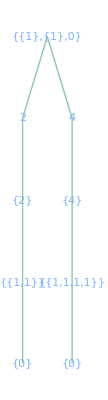

```mathematica
λs={1};
mλs={1};
ν=0;
dMax=4;
tree=GrowMultiplicitySpaceTree[λs,mλs,ν,Range[dMax]]
```

This tree encodes the direct sum structure in Eq. (1) and can be interpreted as follows.

Level | Symbol | Meaning
0(root) | {(λ)_λ,(dim M_λ)_λ,ν} | concise representation for X=⊕_λ H_λ⊗M_λ and Y=H_ν
1 | D | total degree of the polynomial in 𝒮^D(X)
2 | (d_λ)_λ | multidegree in the H_λ:total number of vector/matrix/3–tensor/… terms in the polynomial irrespective of multiplicity
3 | (π_λ)_λ | partitions determining the partial symmetry of tensors
4(leaf) | (μ_λ)_λ | the intermediate spins that are directly coupled to H_ν

Using the tree, we simplify Eq. (1) to

(𝒮^2(X))^G≅H_0⊗Hom_G(H_0,H_0)⊗Hom_G(H_0,𝒮^2(H_1))⊗𝒮^2(ℂ^1)≅Hom_G(H_0,𝒮^2(H_1)),
(𝒮^4(X))^G≅H_0⊗Hom_G(H_0,H_0)⊗Hom_G(H_0,𝒮^4(H_1))⊗𝒮^4(ℂ^1)≅Hom_G(H_0,𝒮^4(H_1)),

which can also be seen directly.

The next step is to enumerate bases for all spaces appearing in the simplified versions of Eq. (1) above. The bases for the Hom_G spaces can be represented using Clebsch-Gordan tensors in “spin-tree” format.

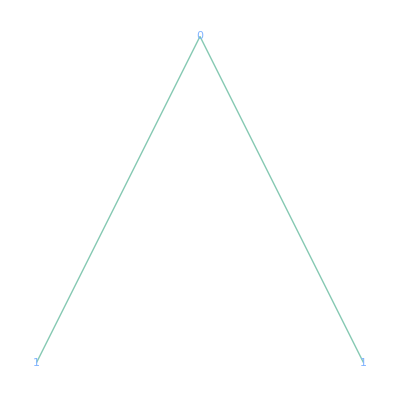

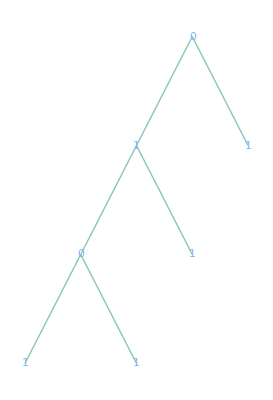

{{{SymmetrizedArray[…]}},{{SymmetrizedArray[…]}}}

```mathematica
arrays=HarvestMultiplicitySpaceTree[tree]
```

To evaluate these polynomials, we turn to Eq. (2),

p(x)∝(H_ν⊗Hom_G(H_ν,⊗_λ H_μ_λ)⊗(⊗_λ Hom_G(H_μ_λ,e_π_λ(H_λ^(⊗d_λ)))⊗_l h_(λ k_(λ l))))_((k_(λ l))_(λ l))·(∏_λ e_π_λ(M_λ^(⊗d_λ))⊗_l m_(λ k_(λ l)))_((k_(λ l))_(λ l)).

In this example, Eq. (2) simplifies to

p_2(x)∝e_{1,1}(H_1^(⊗2))x⊗x,
p_4(x)∝e_{1,1,1,1}(H_1^(⊗4))x⊗x⊗x⊗x,

which is just the evaluation of the fully symmetrized tensor at the input vector x.

```mathematica
Map[test,arrays,{3}]//Factor
```

{{{{-0.57735 (1. x_1 x_2+1. y_1 y_2+1. z_1 z_2)}}},{{{0.111111 (3. x_1 x_2 x_3 x_4+1. x_3 x_4 y_1 y_2+1. x_2 x_4 y_1 y_3+1. x_1 x_4 y_2 y_3+1. x_2 x_3 y_1 y_4+1. x_1 x_3 y_2 y_4+1. x_1 x_2 y_3 y_4+3. y_1 y_2 y_3 y_4+1. x_3 x_4 z_1 z_2+1. y_3 y_4 z_1 z_2+1. x_2 x_4 z_1 z_3+1. y_2 y_4 z_1 z_3+1. x_1 x_4 z_2 z_3+1. y_1 y_4 z_2 z_3+1. x_2 x_3 z_1 z_4+1. y_2 y_3 z_1 z_4+1. x_1 x_3 z_2 z_4+1. y_1 y_3 z_2 z_4+1. x_1 x_2 z_3 z_4+1. y_1 y_2 z_3 z_4+3. z_1 z_2 z_3 z_4)}}}}

Our algorithm recovers the degree 2 and degree 4 scalar invariants of a single vector, namely, (‖x‖)^2 and (‖x‖)^4.

#### Example (Scalar invariants of two vectors: X=H_1⊗ℂ^2, Y=H_0, ν=0, D<=4)

As in the previous example, we simplify Eq. (1) by first enumerating the direct sums in a tree structure.

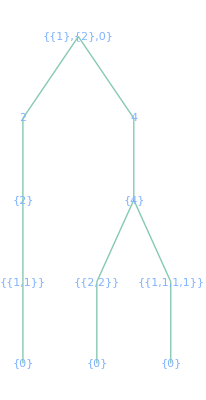

```mathematica
λs={1};
mλs={2};
ν=0;
dMax=4;
tree=GrowMultiplicitySpaceTree[λs,mλs,ν,Range[dMax]]
```

This tells us that

(𝒮^2(X))^G≅H_0⊗Hom_G(H_0,H_0)⊗Hom_G(H_0,𝒮^2(H_1))⊗𝒮^2(ℂ^2)≅Hom_G(H_0,𝒮^2(H_1))⊗𝒮^2(ℂ^2),
(𝒮^4(X))^G≅H_0⊗Hom_G(H_0,H_0)⊗(Hom_G(H_0,e_{2,2}(H_1^(⊗4)))⊗e_{2,2}((ℂ^2)^(⊗4))⊕Hom_G(H_0,𝒮^4(H_1))⊗𝒮^4(ℂ^2))≅Hom_G(H_0,e_{2,2}(H_1^(⊗4)))⊗e_{2,2}((ℂ^2)^(⊗4))⊕Hom_G(H_0,𝒮^4(H_1))⊗𝒮^4(ℂ^2).

We then enumerate “spin-tree” bases for the Hom_G spaces,

-Graphics-

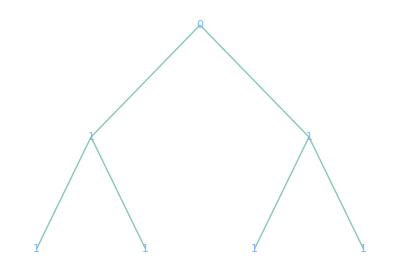

-Graphics-

{{{SymmetrizedArray[…]}},{{SymmetrizedArray[…]}},{{SymmetrizedArray[…]}}}

```mathematica
arrays=HarvestMultiplicitySpaceTree[tree]
```

In this example, Eq. (2) simplifies to

2 of these: SSYT x⊗x and y⊗y. Need to compute the full matrix...!!p_2(x)∝e_{1,1}(H_1^(⊗2))x⊗x,
p_4(x)∝e_{1,1,1,1}(H_1^(⊗4))x⊗x⊗x⊗x,

The first array gives a·a, a·b, and b·b. The second array gives (‖a×b‖)^2. The third array gives (‖a‖)^4, (‖a‖)^2(‖b‖)^2, and (‖b‖)^4.

```mathematica
{a1,a2,a3}=Flatten[arrays,2]
```

{SymmetrizedArray[…],SymmetrizedArray[…],SymmetrizedArray[…]}

```mathematica
test[a1,{1,2}]
```

{-0.57735 x_1 x_2-0.57735 y_1 y_2-0.57735 z_1 z_2}

```mathematica
test[a2,{1,2,1,2}]//Factor
```

{0.288675 (1. x_2^2 y_1^2-2. x_1 x_2 y_1 y_2+1. x_1^2 y_2^2+1. x_2^2 z_1^2+1. y_2^2 z_1^2-2. x_1 x_2 z_1 z_2-2. y_1 y_2 z_1 z_2+1. x_1^2 z_2^2+1. y_1^2 z_2^2)}

```mathematica
test[a3,{1,1,2,2}]//Factor
```

{0.333333 (1. x_1^2 x_2^2+0.333333 x_2^2 y_1^2+1.33333 x_1 x_2 y_1 y_2+0.333333 x_1^2 y_2^2+1. y_1^2 y_2^2+0.333333 x_2^2 z_1^2+0.333333 y_2^2 z_1^2+1.33333 x_1 x_2 z_1 z_2+1.33333 y_1 y_2 z_1 z_2+0.333333 x_1^2 z_2^2+0.333333 y_1^2 z_2^2+1. z_1^2 z_2^2)}

#### Example (Scalar invariants of three vectors: X=H_1⊗ℂ^3, Y=H_0, ν=0, D<=4)

This example reveals the fully antisymmetric Levi-Civita tensor ϵ when three distinct vectors become available as inputs. In the previous examples, not enough vectors were available for ϵ to appear.

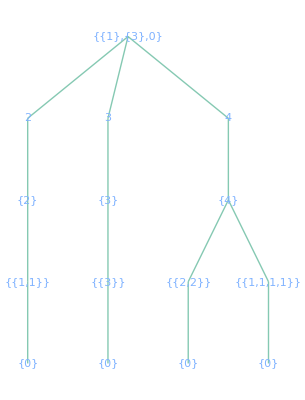

```mathematica
λs={1};
mλs={3};
ν=0;
dMax=4;
tree=GrowMultiplicitySpaceTree[λs,mλs,ν,Range[dMax]]
```

(𝒮^2(X))^G≅H_0⊗Hom_G(H_0,H_0)⊗Hom_G(H_0,𝒮^2(H_1))⊗𝒮^2(ℂ^3)≅Hom_G(H_0,𝒮^2(H_1))⊗𝒮^2(ℂ^3),
(𝒮^3(X))^G≅H_0⊗Hom_G(H_0,H_0)⊗Hom_G(H_0,Λ^3(H_1))⊗Λ^3(ℂ^3)≅Hom_G(H_0,Λ^3(H_1))⊗Λ^3(ℂ^3),
(𝒮^4(X))^G≅H_0⊗Hom_G(H_0,H_0)⊗Hom_G(H_0,𝒮^4(H_1))⊗𝒮^4(ℂ^1)≅Hom_G(H_0,𝒮^4(H_1)).

-Graphics-

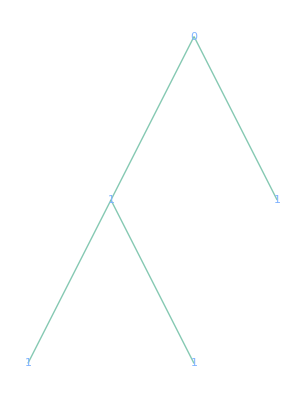

-Graphics-

-Graphics-

{{{SymmetrizedArray[…]}},{{SymmetrizedArray[…]}},{{SymmetrizedArray[…]}},{{SymmetrizedArray[…]}}}

```mathematica
arrays=HarvestMultiplicitySpaceTree[tree]
```

```mathematica
{a1,a2,a3,a4}=Flatten[arrays,2]
```

{SymmetrizedArray[…],SymmetrizedArray[…],SymmetrizedArray[…],SymmetrizedArray[…]}

```mathematica
test[a1,{1,2}]
```

{-0.57735 x_1 x_2-0.57735 y_1 y_2-0.57735 z_1 z_2}

```mathematica
test[a2,{1,2,3}]//Factor//Chop
```

{(0.+0.408248 ⅈ) (1. x_3 y_2 z_1-1. x_2 y_3 z_1-1. x_3 y_1 z_2+1. x_1 y_3 z_2+1. x_2 y_1 z_3-1. x_1 y_2 z_3)}

```mathematica
test[a3,{1,2,1,2}]//Factor
```

{0.288675 (1. x_2^2 y_1^2-2. x_1 x_2 y_1 y_2+1. x_1^2 y_2^2+1. x_2^2 z_1^2+1. y_2^2 z_1^2-2. x_1 x_2 z_1 z_2-2. y_1 y_2 z_1 z_2+1. x_1^2 z_2^2+1. y_1^2 z_2^2)}

```mathematica
test[a4,{1,1,1,2}]//Factor
```

{0.333333 (1. x_1^3 x_2+1. x_1 x_2 y_1^2+1. x_1^2 y_1 y_2+1. y_1^3 y_2+1. x_1 x_2 z_1^2+1. y_1 y_2 z_1^2+1. x_1^2 z_1 z_2+1. y_1^2 z_1 z_2+1. z_1^3 z_2)}

#### Example (Scalar invariants of one matrix: X=H_2⊗ℂ^1, Y=H_0, ν=0, D<=3)

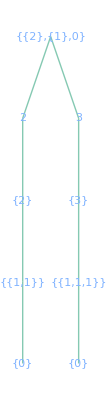

```mathematica
λs={2};
mλs={1};
ν=0;
dMax=3;
tree=GrowMultiplicitySpaceTree[λs,mλs,ν,Range[dMax]]
```

We see that

(𝒮^2(X))^G≅H_0⊗Hom_G(H_0,H_0)⊗Hom_G(H_0,𝒮^2(H_2))⊗𝒮^2(ℂ^1)≅Hom_G(H_0,𝒮^2(H_2)),
(𝒮^3(X))^G≅H_0⊗Hom_G(H_0,H_0)⊗Hom_G(H_0,𝒮^3(H_2))⊗𝒮^3(ℂ^1)≅Hom_G(H_0,𝒮^3(H_2)),

which could have been observed directly.

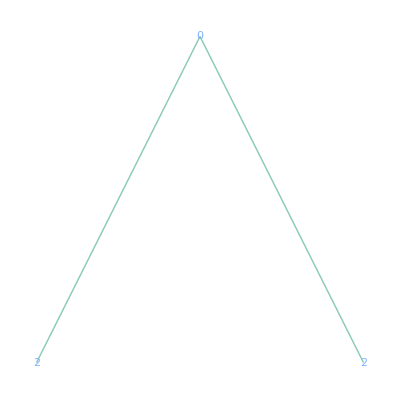

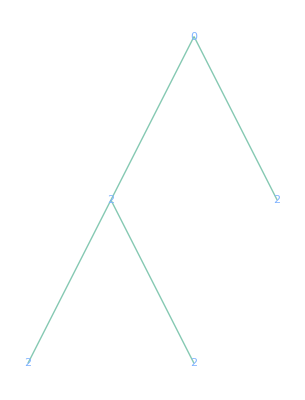

{{{SymmetrizedArray[…]}},{{SymmetrizedArray[…]}}}

```mathematica
arrays=HarvestMultiplicitySpaceTree[tree]
```

### Example

#### Example Code

```mathematica
ClearAll[example]
```

```mathematica
example[λs_,mλs_,ν_,D_,f_]:=
Module[
{tree,numModes,dim=3,labels={i,j,k,l,m,n},a},

tree=GrowMultiplicitySpaceTree[λs,mλs,ν,{D}];
tree=First@First@HarvestMultiplicitySpaceTree[tree];
numModes=Total[λs mλs];
labels=Take[labels,numModes];
a=Symmetrize[Table[Subscript[x,Sequence@@labels],Evaluate[Sequence@@({#,1,dim}&/@labels)]],Symmetric[Range[numModes]]];
FullSimplify[
f[a]/TensorContract[TensorProduct[Sequence@@ConstantArray[a,D],tree],Transpose[Partition[Range[2*numModes*D],numModes*D]]],
If[numModes==2,Tr[a]==0]
]
]
```

#### Example (Degree 2 scalar invariant of a vector)

```mathematica
example[{1},{1},0,2,Total[#^2]&]
```

{(x_1^2+x_2^2+x_3^2)/(-0.57735 x_2^2+1.1547 x_1 x_3)}

#### Example (Degree 2 scalar invariant of a matrix)

```mathematica
example[{2},{1},0,2,Tr[#.#]&]
```

TensorContract::lvrank: Cannot contract level 8 because rank is 7.

(2 x_(1,1)^2+(x_(1,2)+x_(2,1))^2+2 x_(2,2)^2+(x_(1,3)+x_(3,1))^2+(x_(2,3)+x_(3,2))^2+2 x_(3,3)^2)/(2 TensorContract[SymmetrizedArray[…],{{1,5},{2,6},{3,7},{4,8}}])

#### Example (Degree 3 scalar invariant of a matrix)

```mathematica
example[{2},{1},0,3,Det[#]&]
```

TensorContract::lvrank: Cannot contract level 11 because rank is 10.

((x_(1,3)+x_(3,1)) (-2 x_(2,2) (x_(1,3)+x_(3,1))+(x_(1,2)+x_(2,1)) (x_(2,3)+x_(3,2)))+8 (-1/4 (x_(1,2)+x_(2,1))^2+x_(1,1) x_(2,2)) x_(3,3)+(x_(2,3)+x_(3,2)) ((x_(1,2)+x_(2,1)) (x_(1,3)+x_(3,1))+2 (x_(2,3)+x_(3,2)) (x_(2,2)+x_(3,3))))/(8 TensorContract[SymmetrizedArray[…],{{1,7},{2,8},{3,9},{4,10},{5,11},{6,12}}])

## Nakayama’s Lemma

#### Problem

Find bases for R as an ℝ-algebra and M as an R-module.

#### Lemma (Nakayama)

Let M=⊕_(D∈ℕ_0)M^D be a finitely generated graded module over a graded ring R=⊕_(D∈ℕ_0)R^D, where R_0=ℝ. Let I:=⊕_(D∈ℕ)R^D be the ideal generated by the positively graded elements of R. Let L⊆M. Then L/I M generates M/I M as an ℝ-module iff L generates M as an R-module.

#### Algorithm

Suppose that we are given bases ℛ_D,ℳ_D for R^D,M^D as ℝ-modules. Note that

(I M)^D:=I M∩M^D=∑_(1<=D'<=D) R_D' M_(D-D'),
I M=⊕_(D∈ℕ)(I M)^D,
M/I M≅⊕_(D∈ℕ)M^D/(I M)^D.

Moreover,

(I M)^D=Span{r_D' m_(D-D')|1<=D'<=D,r_D'∈ℛ_D',m_(D-D')∈ℳ_(D-D')}.

Now, define

D_max:=max{D∈ℕ|M^D/(I M)^D!=0},

We have a Hilbert series for M_D, we need one for (I M)_D to get these degrees.

which may be difficult to determine in practice. For each 1<=D<=D_max, compute a basis for (I M)_D and extend it to a basis for M^D by adjoining the basis vectors in the set L_D⊆M^D. Write L:=∪_(D∈ℕ)L_D. Since L_D/(I M)_D is a basis for M^D/(I M)_D, L/I M is a basis for M/I M, so by Nakayama’s Lemma, L is a minimal generating set for M as an R-module.

Next, apply the above algorithm with M=I. Let ℝ[L] be the ℝ-algebra generated by L. Clearly, ℝ⊆ℝ[L]. Now, write R_(<=D):=R_0⊕…⊕R^D, and suppose that R_(<=D)⊆ℝ[L]. Then

R_(D+1)=I_(D+1)⊆Span_ℝ(L_(D+1))+(I^2)_(D+1)=Span_ℝ(L_(D+1))+∑_(1<=D'<=D) I_D' I_(D+1-D').

Clearly, Span_ℝ(L_(D+1))⊆ℝ[L], and by the inductive hypothesis, I_1,...,I_D⊆R_(<=D)⊆ℝ[L]. Thus, R=ℝ[L]. To see that L is minimal, note that if any L⊆I generates R as an ℝ-algebra, then L generates I as an R-module, so L/I^2 generates I/I^2 as an ℝ-module. Thus, since our given L makes L/I^2 a basis for I/I^2, our given L is a minimal generating set for R as an ℝ-algebra.

## References

[W03]	https://doi.org/10.1017/CBO9780511546556

## Proofs

#### Proposition (Change of basis from angular to monomial)

The iterated Clebsch-Gordan tensor converts the angular momentum basis on H_λ to the angular momentum basis on H_1^(⊗λ). Let U:H_1->H_1 convert the angular momentum basis on H_1 to the monomial basis on H_1. Then U^(⊗λ) converts the angular momentum basis on H_1^(⊗λ) to the monomial basis on H_1^(⊗λ). These should still be symmetric and trace free, hence they should form a monomial basis for H_λ⊆H_1^(⊗λ).

#### Question for Prof. Damiolini

Let H_λ be the SO(3)-irrep of dimension 2λ+1. Let d∈ℕ, let π be a partition of d, and let e_π be a Young symmetrizer with shape π. Iterated Clebsch-Gordan yields the isotypic decomposition

H_λ^(⊗d)≅⊕_μ H_μ⊗Hom_(SO(3))(H_μ,H_λ^(⊗d)).

Moreover, a basis for the multiplicity space Hom_(SO(3))(H_μ,H_λ^(⊗d)) is parameterized by the collection of valid paths γ:=(γ_1,γ_2,...,γ_d) starting at γ_1=λ and ending at γ_d=μ, where each valid path γ corresponds to the tensor

CG(γ):=∏_(j=1)^(d-1) (γ_j | λ | γ_(j+1)
s_j | m_(j+1) | s_(j+1))∈Hom_(SO(3))(H_μ,H_λ^(⊗d)),
s_j:=m_1+…+m_j.

We are interested in the isotypic decomposition after applying the Young symmetrizer,

e_π(H_λ^(⊗d))≅⊕_μ H_μ⊗Hom_(SO(3))(H_μ,e_π(H_λ^(⊗d))).

In particular, our goal is to parameterize an basis for Hom_(SO(3))(H_μ,e_π(H_λ^(⊗d))) in a way analogous to the above for Hom_(SO(3))(H_μ,H_λ^(⊗d)). One method is to directly compute the spanning set {e_π(CG(γ))}_γ and extract a basis, but this method is slow; many e_π(CG(γ)) are zero, and even those that are nonzero may have linear dependencies (in addition, the zero/nonzero pattern seems complicated).

## Temp Storage

```mathematica
TensorMultiplyStep[tensor_,{reverseLeaf_,reverseRank_,reverseAccRank_}]:=TensorContract[TensorProduct[reverseLeaf,tensor],{{reverseRank,reverseAccRank}}]
```

```mathematica
OuterTensorMultiply[leaves_,roots_]:=Flatten[Outer[TensorMultiply,Tuples[leaves],roots,1],1]
```

```mathematica
TensorMultiply[leaf_,root_]:=
Module[
{n=Length[leaf],reverseLeaf,reverseRank,reverseAccRank},
reverseLeaf=Reverse[leaf];
reverseRank=TensorRank/@reverseLeaf;
reverseAccRank=Accumulate[reverseRank]+Range[n,-n+2,-2];
Fold[
TensorMultiplyStep,
root,
Transpose[{reverseLeaf,reverseRank,reverseAccRank}]
]
]
```

### asdf

```mathematica
ClearAll[
NonzeroQ,
computeTable,
plotTable,
gridTable
]
```

```mathematica
NonzeroQ[array_]:=Boole[Total[Abs@Chop@N@array,∞]!=0]
```

```mathematica
computeTable[λ_,p_,μ_]:=
Module[
{paths,tensors},

paths=ClebschGordanPathsSchurPower[λ,p,μ];
tensors=TensorBasisSchurPower[λ,p,μ];

{{{IsotypicMultiplicitySchurPower[λ,p,μ]}},Flatten[Last@paths,1],{Map[NonzeroQ,tensors]}}
]
```

```mathematica
plotTable[{πs_,βs_,table_}]:=
Module[
{rowTicks,colnTicks},

rowTicks=Transpose[{Range[Length[πs]],πs}];
colnTicks=Transpose[{Range[Length[βs]],MatrixForm/@βs}];

ArrayPlot[table,FrameTicks->{rowTicks,Range[Length[βs]],Range[Length[πs]],colnTicks},Mesh->True,Frame->True,ImageSize->1->32]
]
```

```mathematica
Table[f[λ,p,μ],{λ,1,3},{d,1,3},{p,IntegerPartitions[d,{1},Range[3]]},{μ,IsotypicComponentsSchurPower[λ,p]}];
```

```mathematica
Map[plotTable,%,{4}]
```

#### Theorem (Schur-Weyl duality)

Let V be a finite dimensional vector space, let the general linear group GL(V) act diagonally on V^(⊗d), and let the symmetric group S^d act via factor permutation on V^(⊗d). Then

V^(⊗d)≅⊕_π e_π(V^(⊗d))⊗[π],

where the sum is over all integer partitions π of d with at most dim V parts.

```mathematica
Options[AncestralNestTree]=Options[Tree];
AncestralNestTree[f_,t_,opts:OptionsPattern[]]:=
TreeReplacePart[
t,
Function[
pos,
{pos}:>Tree[
First@TreeExtract[t,{pos},TreeData],
Tree[#,None]&/@f[TreeExtract[t,Take[pos,#]&/@Range[0,Length@pos],TreeData]]
]
]/@TreePosition[t,_,"Leaves"],
opts
]
```

```mathematica
Abs[ListConvolve[{1,-1},γs]]\[VectorLessEqual]Rest[λs]\[VectorLessEqual]ListConvolve[{1,1},γs]
```

#### Scratch

We know that

⊕_ν H_ν⊗VP_ν^(d+1)≅H_λ^(⊗d+1)≅⊕_μ H_μ⊗H_λ⊗VP_μ^(λ,d)≅⊕_ν H_ν⊗⊕_(|μ-ν|<=λ)VP_μ^(λ,d),

so

⊕_(|μ-ν|<=λ)VP_μ^d≅VP_ν^(d+1)

via

(λ,…,μ)↦(λ,…,μ,ν).

We know that

⊕_μ H_μ⊗VP_μ^d≅H_λ^(⊗d)≅⊕_(π⊢d)e_π(H_λ^(⊗d))⊗[π]≅⊕_(π⊢d)⊕_μ H_μ⊗e_(π,μ)(VP_μ^d)⊗[π]≅⊕_μ H_μ⊗(⊕_(π⊢d)e_(π,μ)(VP_μ^d)⊗[π]),

so

VP_μ^d≅⊕_(π⊢d)e_(π,μ)(VP_μ^d)⊗[π].

Thus,

⊕_(|μ-ν|<=λ)⊕_(π⊢d)e_(π,μ)(VP_μ^d)⊗[π]≅⊕_(π'⊢d+1)e_(π',ν)(VP_ν^(d+1))⊗[π'].

J_1:=(  |   |  
  |   | -ⅈ
  | ⅈ |  ),J_2:=(  |   | ⅈ
  |   |  
-ⅈ |   |  ),J_3:=(  | -ⅈ |  
ⅈ |   |  
  |   |  ),J_±:=1/(√2)(J_1±ⅈ J_2)=1/(√2)(  |   | ∓1
  |   | -ⅈ
±1 | ⅈ |  ).

Definition: Let

A:=⊕_(Y irrep of G)(𝒮(X^*)⊗Y)^G

be the covariant algebra of X.

Remark: For certain specific X, Sahil has obtained (non-minimal) generating sets for A as an ℝ-algebra. These generating sets can be cut down to generating sets for M as an R-module, but the process is computationally expensive.

Definition:  The tensor algebra on V is the graded ℝ-algebra

𝒯(V):=⊕_(d∈ℕ_0)𝒯^d(V),
𝒯^d(V):=V^(⊗d).

The symmetrization map on 𝒯(V) is the linear map

Sym:𝒯(V)->𝒯(V),
v_1⊗…⊗v_d↦1/(d!)∑_(σ∈Σ_d) v_(σ(1))⊗…⊗v_(σ(d)).

The symmetric algebra on V is the commutative graded ℝ-algebra

𝒮(V):=Sym(𝒯(V))=⊕_(d∈ℕ_0)𝒮^d(V),
𝒮^d(V):=Sym(𝒯^d(V)),

with multiplication given by the shuffle product

⊙:𝒮(V)×𝒮(V)->𝒮(V),
(a,b)↦a⊙b:=Sym(a⊗b).

Lemma: Let G act linearly on vector spaces V,{V_α}_α. Then

g∈G acts on φ∈V^* by g φ:=φ∘g^-1,

g∈G acts on ⊕_α v_α∈⊕_α V_α by g⊕_α v_α:=⊕_α g v_α, and

g∈G acts on ⊗_α v_α∈⊗_α V_α by g⊗_α v_α:=⊗_α g v_α provided that the tensor product over α is finite.

Moreover, with respect to the above actions, there exist equivariant isomorphisms (which necessarily have equivariant inverses)

(⊕_α V_α)⊗V≅⊕_α(V_α⊗V) and

(⊕_α V_α)^*≅⊕_α V_α^* provided that the sum over α is finite.

Lemma: Let V,M be representations of G.

If M is fixed by G, then (V⊗M)^G=V^G⊗M.

Hom(V,M)≅(V^*⊗M)^G.

Lemma (Schur): Let V,W be irreducible representations of G, and let φ∈Hom(V,W). Then φ=0 or φ is an isomorphism. In particular, either Hom(V,W)=0 or Hom(V,W)≅ℂ.

Proposition: R is a graded subalgebra of 𝒮(X^*). If conditions, then M is a finitely generated graded R-module.

Proof: First, note that

R:=(𝒮(X^*))^G=⊕_(d∈ℕ_0)(𝒮^d(X^*))^G.

Thus, R is a graded subspace of S(X^*). Moreover, since the tensor product and the symmetrization map are equivariant, the shuffle product is equivariant, so R is closed under multiplication, and moreover the multiplication respects the grading.

Next, define the scalar multiplication

R×M->M
(r,φ⊗y)↦(r⊙φ)⊗y

on elementary tensors in M, and extend the multiplication linearly to all of M. Since the shuffle product is equivariant, the scalar multiplication is well defined. That M is a graded R-module follows easily. That M is finitely generated follows from conditions.

Given ℛ_D,ℳ_D for all D=0,1,2,...

For D=1,2,...

For D'=1,2,...,D

For r_D'∈ℛ_D',m_(D-D')∈ℳ_(D-D'), multiply r_D' with m_(D-D') as monomials

#### Reduce to finding a basis for the subspace of monomials

Theorem 1 (https://arxiv.org/abs/2406.01552): Write X as the direct sum

X=⊕_(j=1)^J X_j

of irreducible representations X_j. There exists an equivariant isomorphism of graded ℝ-algebras

𝒮(X^*)≅⊕_(d∈ℕ_0)⊕_(1<=j_1<=…<=j_d<=J)X_j_1^*⊗…⊗X_j_d^*,

which restricts to an equivariant isomorphism of graded ℝ-algebras

R=(𝒮(X^*))^G≅⊕_(d∈ℕ_0)⊕_(1<=j_1<=…<=j_d<=J)(X_j_1^*⊗…⊗X_j_d^*)^G.

There exists an equivariant isomorphism of graded ℝ-modules and graded R-modules

𝒮(X^*)⊗Y≅⊕_(d∈ℕ_0)⊕_(1<=j_1<=…<=j_d<=J)X_j_1^*⊗…⊗X_j_d^*⊗Y,

which restricts to an equivariant isomorphism of graded ℝ-modules and graded R-modules

M=(𝒮(X^*)⊗Y)^G≅⊕_(d∈ℕ_0)⊕_(1<=j_1<=…<=j_d<=J)(X_j_1^*⊗…⊗X_j_d^*⊗Y)^G.

Proof: First, observe that

𝒯(X^*)=⊕_(d∈ℕ_0)𝒯^d(X^*)=⊕_(d∈ℕ_0)(X^*)^(⊗d)≅⊕_(d∈ℕ_0)(⊕_(j=1)^J X_j^*)^(⊗d)≅⊕_(d∈ℕ_0)⊕_(j_1,…,j_d=1)^J X_j_1^*⊗…⊗X_j_d^*,

where the multiplication on the right-hand side is still the ordinary tensor product. Symmetrizing yields Eq. (1),

𝒮(X^*)≅⊕_(d∈ℕ_0)⊕_(1<=j_1<=…<=j_d<=J)X_j_1^*⊗…⊗X_j_d^*,

where the multiplication on the right-hand side is defined by declaring the product of X_j_1^*⊗…⊗X_j_d^* and X_k_1^*⊗…⊗X_k_e^* to be X_j_1^*⊗…⊗X_j_d^*⊗X_k_1^*⊗…⊗X_k_e^* with the indices reordered to be nondecreasing.

Corollary: The monomial parts of an equivariant polynomial are equivariant.

𝒮^d_λ(H_λ⊗M_λ)=((H_λ⊗M_λ)^(⊗d_λ))^(𝔖^d_λ)≅(H_λ^(⊗d_λ)⊗M_λ^(⊗d_λ))^(𝔖^d_λ)
≅^(Schur-Weyl duality)((⊕_(π∈P(d_λ,h_λ))e_π(H_λ^(⊗d_λ))⊗[π])⊗(⊕_(π∈P(d_λ,m_λ))e_π(M_λ^(⊗d_λ))⊗[π]))^(𝔖^d_λ)
≅^(Schur Lemma)⊕_(π⊢d_λ)e_π(H_λ^(⊗d_λ))⊗e_π(M_λ^(⊗d_λ)),

## Draft Stuff (Old)

```mathematica
changeBasis[λ_Integer?NonNegative]:=
SparseArray@Switch[
λ,
0,{1},
1,({
 {1/Sqrt[2], 0, -(1/Sqrt[2])},
 {-(I/Sqrt[2]), 0, -(I/Sqrt[2])},
 {0, 1, 0}
}),
_,TensorMultiply[ConstantArray[changeBasis[1],λ],ClebschGordanTensor[ConstantArray[1,λ],Range[λ]]]
]
```

```mathematica
HarvestPaths[t_,f_]:=Function[pos,f[TreeExtract[t,Take[pos,#]&/@Range[0,Length@pos],TreeData]]]/@TreePosition[t,_,"Leaves"]
```

```mathematica
testing[λ_,p_,μ_]:=Total[IsotypicMultiplicityTensorProduct[#,μ]&/@Select[Tuples@IsotypicComponentsExteriorPower[λ,p],IsotypicComponentTensorProductQ[#,μ]&]]
```

```mathematica
dims[{{λs_,mλs_,ν_},D_,dλs_,πλs_,μλs_}]:=IsotypicMultiplicityTensorProduct[μλs,ν]*Times@@MapThread[IsotypicMultiplicitySchurPower,{λs,πλs,μλs}]
```

```mathematica
dimsbig[{{λs_,mλs_,ν_},D_,dλs_,πλs_,μλs_}]:=IsotypicMultiplicityTensorProduct[μλs,ν]*Times@@MapThread[testing,{λs,πλs,μλs}]
```

#### Find a basis for (ℋ^λ(V))^(SO(3))

Definition: Let 𝒫_(O(V))(m) denote the set of perfect matchings of {1,...,m}. For any P={{i_1,j_1},...,{i_l,j_l}}∈𝒫_(O(V))(m), define σ_P∈S_(2l) to be the permutation whose two-line notation is

σ_P:=(1 | 2 | … | 2l-1 | 2l
i_1 | j_1 | … | i_l | j_l),

where the second row is ordered such that i_m<j_m for all m∈{1,...,l} and i_m<i_(m+1) for all m∈{1,...,l-1}. Further define T_P∈𝒯^m(V) to be the tensor

T_P:=σ_P((⊕_(i,j=1)^(dim V)δ_(i j)e_i⊗e_j)^(⊗l)).

Lemma 2: The set

{T_P}_(P∈𝒫_(O(V))(m))

is a basis for (𝒯^m(V))^(O(V)) of size ((2l)!)/(2^l l!).

Definition: Let 𝒫_(SO(V))(m) denote the set of non-crossing planar partitions of {1,...,m} with no singletons. For any P={B_1,...,B_j}∈𝒫_(SO(V))(m), define

T_P:=

Lemma 3: The set

{T_P}_(P∈𝒫_(SO(V))(m))

is a basis for (𝒯^m(V))^(SO(V)) of size [m^th Riordan number].

#### Find a basis for the subspace of monomials

Remark 6: Problem 3 has been solved for X_j=𝒯^d_j(V), Y=𝒯^d(V), and G=O(V) in https://arxiv.org/abs/2406.01552. I think Problem 3 has also been solved for X_j=𝒯^d_j(V), Y=𝒯^d(V), and G=SO(V).

Remark 8: Appendix A in https://arxiv.org/pdf/2404.18735 shows that any invariant polynomial 𝒮^d(V)->ℝ is the restriction of an invariant polynomial 𝒯^d(V)->ℝ (however, there are polynomial extensions that are not invariant). Results like this might help.